## Altarelli and Feruglio (2006) 0512103v2 Tri-Bimaximal Neutrino Mixing, A_4 and the Modular Symmetry

### [Prep] Definitions of A_4 representations

The U matrix is the neutrino mixing matrix that is approximately in the tri-bimaximal form

```mathematica
U=MatrixForm[{{Sqrt[2/3],1/Sqrt[3],0},{-1/Sqrt[6],1/Sqrt[3],-1/Sqrt[2]},{-1/Sqrt[6],1/Sqrt[3],1/Sqrt[2]}}]
```

(√(2/3) | 1/(√3) | 0
-1/(√6) | 1/(√3) | -1/(√2)
-1/(√6) | 1/(√3) | 1/(√2))

In this study we are interested in the A_4 group with generators T and S following  < S,T | S^2=(ST)^3=T^3=1 > . A particular choice of irrep special up to similarity

```mathematica
T=DiagonalMatrix[{1,ω^2,ω}]/.{ω->E^(-2π I/3)}
```

{{1,0,0},{0,ⅇ^((2 ⅈ π)/3),0},{0,0,ⅇ^(-(2 ⅈ π)/3)}}

```mathematica
S=1/3{{-1,2,2},{2,-1,2},{2,2,-1}}
```

{{-1/3,2/3,2/3},{2/3,-1/3,2/3},{2/3,2/3,-1/3}}

Check the transformation rule:

```mathematica
T^3//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
MatrixForm/@{S.S,T.T.T}
```

{(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}

The idea is to create objects that transforms as a singlet/triplet under some transformation of choice

### [Prep] Constructing singlets and triplets using a , b

Consider two fields a and b transforming under A_4 irrep

```mathematica
a={a1,a2,a3};
b={b1,b2,b3};
```

```mathematica
SMap[v_]:=Table[v[[i]]->target/.{target->(S.v)[[i]]},{i,{1,2,3}}]
TMap[v_]:=Table[v[[i]]->target/.{target->(T.v)[[i]]},{i,{1,2,3}}]
```

We can check that the following objects transform as singlets of 1, 1’,  1’’ under T

```mathematica
singlet0=a1 b1+a2 b3+a3 b2;
singlet1=a3 b3+a1 b2+a2 b1;
singlet2=a2 b2+a1 b3+a3 b1;
```

```mathematica
{singlet0,singlet1,singlet2}/.Flatten[{TMap[a],TMap[b]}]//Simplify
```

{a1 b1+a3 b2+a2 b3,(-1)^(2/3) (a2 b1+a1 b2+a3 b3),-(-1)^(1/3) (a3 b1+a2 b2+a1 b3)}

```mathematica
%/.{a1 b1+a2 b3+a3 b2->s0,a3 b3+a1 b2+a2 b1->s1,a2 b2+a1 b3+a3 b1->s2}
```

{s0,(-1)^(2/3) s1,-(-1)^(1/3) s2}

The three singlets transform trivially under S

```mathematica
{singlet0,singlet1,singlet2}/.Flatten[{SMap[a],SMap[b]}]//Simplify
```

{a1 b1+a3 b2+a2 b3,a2 b1+a1 b2+a3 b3,a3 b1+a2 b2+a1 b3}

Let’s check how the triplets and anti-triplet transform

```mathematica
triplet=1/3{2a1 b1-a2 b3-a3 b2,2a3 b3-a1 b2-a2 b1,2a2 b2-a1 b3-a3 b1};
tripletp=1/2{a2 b3-a3 b2,a1 b2-a2 b1,a1 b3-a3 b1};
```

The triplet transforms by v->T v under the T map

```mathematica
{triplet,tripletp}/.Flatten[{TMap[a],TMap[b]}]//Simplify
```

{{1/3 (2 a1 b1-a3 b2-a2 b3),-1/3 (-1)^(2/3) (a2 b1+a1 b2-2 a3 b3),1/3 (-1)^(1/3) (a3 b1-2 a2 b2+a1 b3)},{1/2 (-a3 b2+a2 b3),1/2 (-1)^(2/3) (-a2 b1+a1 b2),1/2 (-1)^(1/3) (a3 b1-a1 b3)}}

The triplet transforms by v->S v under the S map

```mathematica
triplet/.Flatten[{SMap[a],SMap[b]}]//Expand
```

{-(2 a1 b1)/9-(2 a2 b1)/9-(2 a3 b1)/9-(2 a1 b2)/9+(4 a2 b2)/9+(a3 b2)/9-(2 a1 b3)/9+(a2 b3)/9+(4 a3 b3)/9,(4 a1 b1)/9+(a2 b1)/9-(2 a3 b1)/9+(a1 b2)/9+(4 a2 b2)/9-(2 a3 b2)/9-(2 a1 b3)/9-(2 a2 b3)/9-(2 a3 b3)/9,(4 a1 b1)/9-(2 a2 b1)/9+(a3 b1)/9-(2 a1 b2)/9-(2 a2 b2)/9-(2 a3 b2)/9+(a1 b3)/9-(2 a2 b3)/9+(4 a3 b3)/9}

### Define singlet and triplet products between fields

```mathematica
singletProduct[x_,y_]:=Module[{a1,a2,a3,b1,b2,b3},
a1=x[[1]];a2=x[[2]];a3=x[[3]];b1=y[[1]];b2=y[[2]];b3=y[[3]];a1 b1+b2 a3+a2 b3]
tripletProduct[x_,y_]:=Module[{a1,a2,a3,b1,b2,b3},
a1=x[[1]];a2=x[[2]];a3=x[[3]];b1=y[[1]];b2=y[[2]];b3=y[[3]];1/3{2a1 b1-a2 b3-a3 b2,2a3 b3-a1 b2-a2 b1,2a2 b2-a1 b3-a3 b1}]
antitripletProduct[x_,y_]:=Module[{a1,a2,a3,b1,b2,b3},
a1=x[[1]];a2=x[[2]];a3=x[[3]];b1=y[[1]];b2=y[[2]];b3=y[[3]];1/2{a2 b3-a3 b2,a1 b2-a2 b1,a1 b3-a3 b1}]
```

### Define ψ^T, ψ^S, ψ_0^T, ψ_0^S fields and their components

```mathematica
sub={ψt0->{t01,t02,t03},ψt->{t1,t2,t3},ψs0->{s01,s02,s03},ψs->{s1,s2,s3}}
```

{ψt0→{t01,t02,t03},ψt→{t1,t2,t3},ψs0→{s01,s02,s03},ψs→{s1,s2,s3}}

### Define the driving potential w_d

```mathematica
wd=M(singletProduct[ψt0,ψt])+g singletProduct[ψt0,tripletProduct[ψt,ψt]]+g1 singletProduct[ψs0,tripletProduct[ψs,ψs]]+g2 ξt singletProduct[ψs0,ψs]+g3 ξ0 singletProduct[ψs,ψs]+g4 ξ0 ξ^2+g5 ξ0 ξ ξt+g6 ξ0 ξt^2;
```

### Vacuum alignment equations from potential minimisation

```mathematica
equationTable=Insert[Table[{dWd/(d v),D[wd/.sub,v]==0},{v,{t01,t02,t03,s01,s02,s03}}],{dWd/dξ0,D[wd/.sub,ξ0]==0},-1];
Grid[equationTable,Frame->All]
alignmentEquations=Transpose[equationTable][[2]];
```

dWd/(d t01) | M t1+1/3 g (2 t1^2-2 t2 t3)==0
dWd/(d t02) | M t3+1/3 g (2 t2^2-2 t1 t3)==0
dWd/(d t03) | M t2+1/3 g (-2 t1 t2+2 t3^2)==0
dWd/(d s01) | 1/3 g1 (2 s1^2-2 s2 s3)+g2 s1 ξt==0
dWd/(d s02) | 1/3 g1 (2 s2^2-2 s1 s3)+g2 s3 ξt==0
dWd/(d s03) | 1/3 g1 (-2 s1 s2+2 s3^2)+g2 s2 ξt==0
dWd/dξ0 | g3 (s1^2+2 s2 s3)+g4 ξ^2+g5 ξ ξt+g6 ξt^2==0

#### Solve for the vacuum alignment that breaks A_4-> G_T

```mathematica
vacuumPsiT=Solve[alignmentEquations[[1;;3]],{t1,t2,t3}]
```

{{t1→0,t2→0,t3→0},{t1→-(3 M)/(2 g),t2→0,t3→0},{t1→M/(2 g),t2→-M/g,t3→-M/g},{t1→M/(2 g),t2→((-1)^(1/3) M)/g,t3→-((-1)^(2/3) M)/g},{t1→M/(2 g),t2→-((-1)^(2/3) M)/g,t3→((-1)^(1/3) M)/g}}

Apart from the (0,0,0) solution, the other three non-trivial solutions form a Z_3 vacuum manifold. We chose the (1,0,0) direction for convenience

```mathematica
vevGT=vacuumPsiT[[2]]
```

{t1→-(3 M)/(2 g),t2→0,t3→0}

#### Solve for the vacuum alignment that breaks A_4->G_S

The GS vacuum solution depends on the sign of the coupling g1 and g2. 
The programme doesn’t know about the mass term m^2 ξ^2 so we force SSB by g1, g2<0 
We chose m_ξt^2>0, enforcing ξt=0, which we put in the assumption before solving

```mathematica
vacuumPsiS=Solve[alignmentEquations[[4;;7]],{s1,s2,s3},Assumptions->{g1<0,g2<0,ξt==0}]
```

{{s1→-(ⅈ √g4 ξ)/(√3 √g3),s2→-(ⅈ √g4 ξ)/(√3 √g3),s3→-(ⅈ √g4 ξ)/(√3 √g3)},{s1→-(ⅈ √g4 ξ)/(√3 √g3),s2→((-1)^(1/6) √g4 ξ)/(√3 √g3),s3→((-1)^(5/6) √g4 ξ)/(√3 √g3)},{s1→-(ⅈ √g4 ξ)/(√3 √g3),s2→((-1)^(5/6) √g4 ξ)/(√3 √g3),s3→((-1)^(1/6) √g4 ξ)/(√3 √g3)},{s1→(ⅈ √g4 ξ)/(√3 √g3),s2→(ⅈ √g4 ξ)/(√3 √g3),s3→(ⅈ √g4 ξ)/(√3 √g3)},{s1→(ⅈ √g4 ξ)/(√3 √g3),s2→-((-1)^(1/6) √g4 ξ)/(√3 √g3),s3→-((-1)^(5/6) √g4 ξ)/(√3 √g3)},{s1→(ⅈ √g4 ξ)/(√3 √g3),s2→-((-1)^(5/6) √g4 ξ)/(√3 √g3),s3→-((-1)^(1/6) √g4 ξ)/(√3 √g3)}}

The (-1,-1,-1) and (1,1,1) directions and their A4 rotations forms a Z_3 x Z_2 vacuum manifold.  We choose the (1,1,1) direction for convenience.

```mathematica
vevGS=vacuumPsiS[[4]]
```

{s1→(ⅈ √g4 ξ)/(√3 √g3),s2→(ⅈ √g4 ξ)/(√3 √g3),s3→(ⅈ √g4 ξ)/(√3 √g3)}

## Varzielas, Ross, and Talbert (JHEP 2018) A Unified Model of Quarks and Leptons with a Universal Texture

Introduce tri-bimaximal neutrino mixing matrix from Z_2 x Z_2 SSB

```mathematica
Tribi={1/Sqrt[2]{0,1,1},1/Sqrt[3]{1,1,-1},1/Sqrt[6]{2,-1,1}};
%//MatrixForm
```

(0 | 1/(√2) | 1/(√2)
1/(√3) | 1/(√3) | -1/(√3)
√(2/3) | -1/(√6) | 1/(√6))

### Previous work

Define familon scalar fields charged under 3’

```mathematica
preAlignment={θ3->{t30,t31,t32},θ123->{t1230,t1231,t1232},θ23->{t230,t231,t232},θx->{tx0,tx1,tx2}};
(*postAlignment={θ3->{0,0,v3},θ123->v123/Sqrt[3]{E^(I b),E^(I a),-1},θ23->v23/Sqrt[2]{0,E^(I a),1},θx->vx/Sqrt[6]{2 E^(I b),-E^(I a),1}};*)
```

```mathematica
postAlignment={t30->0,t31->0,t32->v3,t1230->v123/Sqrt[3] E^(I b),t1231->v123/Sqrt[3] E^(I a),t1232->-v123/Sqrt[3],t230->0,t231->v23/Sqrt[2] E^(I a),t232->v23/Sqrt[2],tx0->vx/Sqrt[6] 2 E^(I b),tx1->-E^(I a) vx/Sqrt[6],tx2->vx/Sqrt[6]};
```

```mathematica
(*V1=m3^2 Transpose[θ3].θ3+m123^2 Transpose[θ123].θ123;
V2=h3^2(ConjugateTranspose[θ3].θ3)^2 +h123^2(ConjugateTranspose[θ123].θ123)^2 ;
V3=k1 ConjugateTranspose[θx].θ123 ConjugateTranspose[θ123].θx;
V4=k2 m0 Times@@θx;
V5=k3 Transpose[θ23].θx ConjugateTranspose[θ23].Conjugate[θx]+k4 ConjugateTranspose[θ23].θ3 ConjugateTranspose[θ3].θ23;*)
```

Stick in the complex components later:

```mathematica
V1=m3^2 Transpose[θ3].θ3+m123^2 Transpose[θ123].θ123;
V2=h3^2(Transpose[θ3].θ3)^2 +h123^2(Transpose[θ123].θ123)^2 ;
V3=k1 Transpose[θx].θ123 Transpose[θ123].θx;
V4=k2 m0 Times@@θx;
V5=k3 Transpose[θ23].θx Transpose[θ23].θx+k4 Transpose[θ23].θ3 Transpose[θ3].θ23;
```

```mathematica
V=V1+V2+V3+V4+V5
```

k2 m0 θx+m123^2 Transpose[θ123].θ123+h123^2 (Transpose[θ123].θ123)^2+k3 (Transpose[θ23].θx)^2+k4 Transpose[θ23].θ3 Transpose[θ3].θ23+m3^2 Transpose[θ3].θ3+h3^2 (Transpose[θ3].θ3)^2+k1 Transpose[θ123].θx Transpose[θx].θ123

```mathematica
Vpre=V/.preAlignment
```

{m123^2 (t1230^2+t1231^2+t1232^2)+h123^2 (t1230^2+t1231^2+t1232^2)^2+k4 (t230 t30+t231 t31+t232 t32)^2+m3^2 (t30^2+t31^2+t32^2)+h3^2 (t30^2+t31^2+t32^2)^2+k2 m0 tx0+k1 (t1230 tx0+t1231 tx1+t1232 tx2)^2+k3 (t230 tx0+t231 tx1+t232 tx2)^2,m123^2 (t1230^2+t1231^2+t1232^2)+h123^2 (t1230^2+t1231^2+t1232^2)^2+k4 (t230 t30+t231 t31+t232 t32)^2+m3^2 (t30^2+t31^2+t32^2)+h3^2 (t30^2+t31^2+t32^2)^2+k2 m0 tx1+k1 (t1230 tx0+t1231 tx1+t1232 tx2)^2+k3 (t230 tx0+t231 tx1+t232 tx2)^2,m123^2 (t1230^2+t1231^2+t1232^2)+h123^2 (t1230^2+t1231^2+t1232^2)^2+k4 (t230 t30+t231 t31+t232 t32)^2+m3^2 (t30^2+t31^2+t32^2)+h3^2 (t30^2+t31^2+t32^2)^2+k2 m0 tx2+k1 (t1230 tx0+t1231 tx1+t1232 tx2)^2+k3 (t230 tx0+t231 tx1+t232 tx2)^2}

```mathematica
var={t30,t31,t32,t1230,t1231,t1232,t230,t231,t232,tx0,tx1,tx2};
```

```mathematica
FullSimplify[Grad[Vpre,{t30,t31,t32,t1230,t1231,t1232,t230,t231,t232,tx0,tx1,tx2}]/.postAlignment,{a,b,v3,v123,v23,vx}∈Reals]
```

{{0,1/2 ⅇ^(-ⅈ a) k4 v23^2 v3 (1+ⅇ^(2 ⅈ a) Conjugate'[0]),1/2 v3 (4 m3^2+k4 v23^2+4 h3^2 v3^2+(k4 v23^2+4 h3^2 v3^2) Conjugate'[v3]),(ⅇ^(-ⅈ b) (2 h123^2 v123^3+2 ⅇ^(2 ⅈ b) v123 (m123^2+h123^2 v123^2 Conjugate'[(ⅇ^(ⅈ b) v123)/(√3)])))/(√3),(ⅇ^(-ⅈ a) (2 h123^2 v123^3+2 ⅇ^(2 ⅈ a) v123 (m123^2+h123^2 v123^2 Conjugate'[(ⅇ^(ⅈ a) v123)/(√3)])))/(√3),-(2 v123 (m123^2+h123^2 v123^2+h123^2 v123^2 Conjugate'[-v123/(√3)]))/(√3),(ⅇ^(-ⅈ (2 a+b)) (-1+ⅇ^(2 ⅈ a)) k3 v23 vx^2 (ⅇ^(2 ⅈ b)-ⅇ^(2 ⅈ a) Conjugate'[0]))/(3 √2),(ⅈ k3 v23 vx^2 Sin[a] (-1+Conjugate'[(ⅇ^(ⅈ a) v23)/(√2)]))/(3 √2),(ⅇ^(-2 ⅈ a) v23 (-k3 vx^2-ⅇ^(4 ⅈ a) k3 vx^2 Conjugate'[v23/(√2)]+ⅇ^(2 ⅈ a) (6 k4 v3^2+k3 vx^2) (1+Conjugate'[v23/(√2)])))/(6 √2),k2 m0,-(ⅈ k3 v23^2 vx Sin[a] (-1+Conjugate'[-(ⅇ^(ⅈ a) vx)/(√6)]))/(√6),(k3 v23^2 vx Sin[a] (ⅈ Cos[a]+Sin[a]+(-ⅈ Cos[a]+Sin[a]) Conjugate'[vx/(√6)]))/(√6)},{0,1/2 ⅇ^(-ⅈ a) k4 v23^2 v3 (1+ⅇ^(2 ⅈ a) Conjugate'[0]),1/2 v3 (4 m3^2+k4 v23^2+4 h3^2 v3^2+(k4 v23^2+4 h3^2 v3^2) Conjugate'[v3]),(ⅇ^(-ⅈ b) (2 h123^2 v123^3+2 ⅇ^(2 ⅈ b) v123 (m123^2+h123^2 v123^2 Conjugate'[(ⅇ^(ⅈ b) v123)/(√3)])))/(√3),(ⅇ^(-ⅈ a) (2 h123^2 v123^3+2 ⅇ^(2 ⅈ a) v123 (m123^2+h123^2 v123^2 Conjugate'[(ⅇ^(ⅈ a) v123)/(√3)])))/(√3),-(2 v123 (m123^2+h123^2 v123^2+h123^2 v123^2 Conjugate'[-v123/(√3)]))/(√3),(ⅇ^(-ⅈ (2 a+b)) (-1+ⅇ^(2 ⅈ a)) k3 v23 vx^2 (ⅇ^(2 ⅈ b)-ⅇ^(2 ⅈ a) Conjugate'[0]))/(3 √2),(ⅈ k3 v23 vx^2 Sin[a] (-1+Conjugate'[(ⅇ^(ⅈ a) v23)/(√2)]))/(3 √2),(ⅇ^(-2 ⅈ a) v23 (-k3 vx^2-ⅇ^(4 ⅈ a) k3 vx^2 Conjugate'[v23/(√2)]+ⅇ^(2 ⅈ a) (6 k4 v3^2+k3 vx^2) (1+Conjugate'[v23/(√2)])))/(6 √2),0,k2 m0-(ⅈ k3 v23^2 vx Sin[a] (-1+Conjugate'[-(ⅇ^(ⅈ a) vx)/(√6)]))/(√6),(k3 v23^2 vx Sin[a] (ⅈ Cos[a]+Sin[a]+(-ⅈ Cos[a]+Sin[a]) Conjugate'[vx/(√6)]))/(√6)},{0,1/2 ⅇ^(-ⅈ a) k4 v23^2 v3 (1+ⅇ^(2 ⅈ a) Conjugate'[0]),1/2 v3 (4 m3^2+k4 v23^2+4 h3^2 v3^2+(k4 v23^2+4 h3^2 v3^2) Conjugate'[v3]),(ⅇ^(-ⅈ b) (2 h123^2 v123^3+2 ⅇ^(2 ⅈ b) v123 (m123^2+h123^2 v123^2 Conjugate'[(ⅇ^(ⅈ b) v123)/(√3)])))/(√3),(ⅇ^(-ⅈ a) (2 h123^2 v123^3+2 ⅇ^(2 ⅈ a) v123 (m123^2+h123^2 v123^2 Conjugate'[(ⅇ^(ⅈ a) v123)/(√3)])))/(√3),-(2 v123 (m123^2+h123^2 v123^2+h123^2 v123^2 Conjugate'[-v123/(√3)]))/(√3),(ⅇ^(-ⅈ (2 a+b)) (-1+ⅇ^(2 ⅈ a)) k3 v23 vx^2 (ⅇ^(2 ⅈ b)-ⅇ^(2 ⅈ a) Conjugate'[0]))/(3 √2),(ⅈ k3 v23 vx^2 Sin[a] (-1+Conjugate'[(ⅇ^(ⅈ a) v23)/(√2)]))/(3 √2),(ⅇ^(-2 ⅈ a) v23 (-k3 vx^2-ⅇ^(4 ⅈ a) k3 vx^2 Conjugate'[v23/(√2)]+ⅇ^(2 ⅈ a) (6 k4 v3^2+k3 vx^2) (1+Conjugate'[v23/(√2)])))/(6 √2),0,-(ⅈ k3 v23^2 vx Sin[a] (-1+Conjugate'[-(ⅇ^(ⅈ a) vx)/(√6)]))/(√6),k2 m0+(k3 v23^2 vx Sin[a] (ⅈ Cos[a]+Sin[a]))/(√6)-((-1+ⅇ^(2 ⅈ a)) k3 v23^2 vx Conjugate'[vx/(√6)])/(2 √6)}}

```mathematica
Simplify[Conjugate[x] Conjugate[y],{x,y}∈Reals]
```

x y

```mathematica
Simplify[Conjugate[x],x∈Real]
```

Conjugate[x]

```mathematica
D[Conjugate[x],x]
```

Conjugate'[x]

### Define Δ_27 generators

T here stands for the group generators, but are NOT the algebra basis

```mathematica
Ta={{0,1,0},{0,0,1},{1,0,0}};
%//MatrixForm
Tc=DiagonalMatrix[{1,ω^-1,ω}];
%//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)

(1 | 0 | 0
0 | 1/ω | 0
0 | 0 | ω)

#### All generators

```mathematica
Cgenerators=Table[DiagonalMatrix[{ω^l,ω^k,ω^(-l-k)}]//MatrixForm,{l,{0,1,2}},{k,{0,1,2}}]//Grid
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | ω | 0
0 | 0 | 1/ω) | (1 | 0 | 0
0 | ω^2 | 0
0 | 0 | 1/ω^2)
(ω | 0 | 0
0 | 1 | 0
0 | 0 | 1/ω) | (ω | 0 | 0
0 | ω | 0
0 | 0 | 1/ω^2) | (ω | 0 | 0
0 | ω^2 | 0
0 | 0 | 1/ω^3)
(ω^2 | 0 | 0
0 | 1 | 0
0 | 0 | 1/ω^2) | (ω^2 | 0 | 0
0 | ω | 0
0 | 0 | 1/ω^3) | (ω^2 | 0 | 0
0 | ω^2 | 0
0 | 0 | 1/ω^4)

```mathematica
Dgenerators=Table[DiagonalMatrix[{ω^(-l-k),ω^l,ω^k}]//MatrixForm,{l,{0,1,2}},{k,{0,1,2}}]//Grid
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (1/ω | 0 | 0
0 | 1 | 0
0 | 0 | ω) | (1/ω^2 | 0 | 0
0 | 1 | 0
0 | 0 | ω^2)
(1/ω | 0 | 0
0 | ω | 0
0 | 0 | 1) | (1/ω^2 | 0 | 0
0 | ω | 0
0 | 0 | ω) | (1/ω^3 | 0 | 0
0 | ω | 0
0 | 0 | ω^2)
(1/ω^2 | 0 | 0
0 | ω^2 | 0
0 | 0 | 1) | (1/ω^3 | 0 | 0
0 | ω^2 | 0
0 | 0 | ω) | (1/ω^4 | 0 | 0
0 | ω^2 | 0
0 | 0 | ω^2)

### Define the 1_rs singlet products

We usually use 1_00 only, but here we declare the general product

```mathematica
singletProduct27[r_,s_,x_,y_]:=x.MatrixPower[Ta,s].MatrixPower[Tc,r]. y
```

To demonstrate the different products between s and t:

```mathematica
Table[singletProduct27[k,l,{s1,s2,s3},{t1,t2,t3}],{k,{0,1,2}},{l,{0,1,2}}]//TableForm
```

s1 t1+s2 t2+s3 t3 | s3 t1+s1 t2+s2 t3 | s2 t1+s3 t2+s1 t3
s1 t1+(s2 t2)/ω+s3 t3 ω | s3 t1+(s1 t2)/ω+s2 t3 ω | s2 t1+(s3 t2)/ω+s1 t3 ω
s1 t1+(s2 t2)/ω^2+s3 t3 ω^2 | s3 t1+(s1 t2)/ω^2+s2 t3 ω^2 | s2 t1+(s3 t2)/ω^2+s1 t3 ω^2

### Define the 3_q triplet products and singlet triple product

Triplet multiplication has three possibilities labelled as q=0,1,2
The product of triplets (k,l)=(k',l')=(0,±1)  transforms as (k'',l'')=(0,∓1) so this is their ‘complex conjugate’

Triplet representation labelled by q=0,1,2

```mathematica
(*tripletProduct27[q_,x_,y_]:=MatrixPower[Ta,q].DiagonalMatrix[x].MatrixPower[Ta,q].y
Table[tripletProduct27[q,{s1,s2,s3},{t1,t2,t3}]//MatrixForm,{q,{0,1,2}}]*)
```

{(s1 t1
s2 t2
s3 t3),(s2 t3
s3 t1
s1 t2),(s3 t2
s1 t3
s2 t1)}

Triplet representation symmetrized and antisymmetrized labelled by q=0,1,2

```mathematica
tripletProduct27[q_,x_,y_]:=1/2(MatrixPower[Ta,q].DiagonalMatrix[x].MatrixPower[Ta,q].y+(-1)^q MatrixPower[Ta,2q].DiagonalMatrix[x].MatrixPower[Ta,2q].y)
Table[tripletProduct27[q,{s1,s2,s3},{t1,t2,t3}]//MatrixForm,{q,{0,1,2}}]
```

{(s1 t1
s2 t2
s3 t3),(1/2 (-s3 t2+s2 t3)
1/2 (s3 t1-s1 t3)
1/2 (-s2 t1+s1 t2)),(1/2 (s3 t2+s2 t3)
1/2 (s3 t1+s1 t3)
1/2 (s2 t1+s1 t2))}

Finally, we can construct a singlet with 3 triplets, for convenience we will declare

```mathematica
singletTripleProduct27[r_,s_,q_,x_,y_,z_]:=z.MatrixPower[Ta,s+q].DiagonalMatrix[MatrixPower[Tc,r].y].MatrixPower[Ta,q].x
```

Here, the q stands for three possibilities, where as the r and s label the 9 different singlets.

#### Demonstrate the triplet products q=0,1,2 between s and t

```mathematica
(*Table[tripletProduct27[q,{s1,s2,s3},{t1,t2,t3}]//MatrixForm,{q,{0,1,2}}]*)
```

{(s1 t1
s2 t2
s3 t3),(s2 t3
s3 t1
s1 t2),(s3 t2
s1 t3
s2 t1)}

```mathematica
Table[tripletProduct27[q,{s1,s2,s3},{t1,t2,t3}]//MatrixForm,{q,{0,1,2}}]
```

{(s1 t1
s2 t2
s3 t3),(1/2 (-s3 t2+s2 t3)
1/2 (s3 t1-s1 t3)
1/2 (-s2 t1+s1 t2)),(1/2 (s3 t2+s2 t3)
1/2 (s3 t1+s1 t3)
1/2 (s2 t1+s1 t2))}

#### Demonstrate the 9 singlet triple products for q=0 between s, t, and u

```mathematica
Table[singletTripleProduct27[k,l,0,{s1,s2,s3},{t1,t2,t3},{u1,u2,u3}],{k,{0,1,2}},{l,{0,1,2}}]//TableForm
Table[singletTripleProduct27[k,l,1,{s1,s2,s3},{t1,t2,t3},{u1,u2,u3}],{k,{0,1,2}},{l,{0,1,2}}]//TableForm
Table[singletTripleProduct27[k,l,2,{s1,s2,s3},{t1,t2,t3},{u1,u2,u3}],{k,{0,1,2}},{l,{0,1,2}}]//TableForm
```

s1 t1 u1+s2 t2 u2+s3 t3 u3 | s2 t2 u1+s3 t3 u2+s1 t1 u3 | s3 t3 u1+s1 t1 u2+s2 t2 u3
s1 t1 u1+(s2 t2 u2)/ω+s3 t3 u3 ω | s1 t1 u3+(s2 t2 u1)/ω+s3 t3 u2 ω | s1 t1 u2+(s2 t2 u3)/ω+s3 t3 u1 ω
s1 t1 u1+(s2 t2 u2)/ω^2+s3 t3 u3 ω^2 | s1 t1 u3+(s2 t2 u1)/ω^2+s3 t3 u2 ω^2 | s1 t1 u2+(s2 t2 u3)/ω^2+s3 t3 u1 ω^2

s3 t2 u1+s1 t3 u2+s2 t1 u3 | s1 t3 u1+s2 t1 u2+s3 t2 u3 | s2 t1 u1+s3 t2 u2+s1 t3 u3
s2 t1 u3+(s3 t2 u1)/ω+s1 t3 u2 ω | s2 t1 u2+(s3 t2 u3)/ω+s1 t3 u1 ω | s2 t1 u1+(s3 t2 u2)/ω+s1 t3 u3 ω
s2 t1 u3+(s3 t2 u1)/ω^2+s1 t3 u2 ω^2 | s2 t1 u2+(s3 t2 u3)/ω^2+s1 t3 u1 ω^2 | s2 t1 u1+(s3 t2 u2)/ω^2+s1 t3 u3 ω^2

s2 t3 u1+s3 t1 u2+s1 t2 u3 | s3 t1 u1+s1 t2 u2+s2 t3 u3 | s1 t2 u1+s2 t3 u2+s3 t1 u3
s3 t1 u2+(s1 t2 u3)/ω+s2 t3 u1 ω | s3 t1 u1+(s1 t2 u2)/ω+s2 t3 u3 ω | s3 t1 u3+(s1 t2 u1)/ω+s2 t3 u2 ω
s3 t1 u2+(s1 t2 u3)/ω^2+s2 t3 u1 ω^2 | s3 t1 u1+(s1 t2 u2)/ω^2+s2 t3 u3 ω^2 | s3 t1 u3+(s1 t2 u1)/ω^2+s2 t3 u2 ω^2

Typically, we only use q=0 and we choose r,s=0 if not declared otherwise

### Define potential V_(1,2,3,4,5) and fields θ_(3,23,123,X)

Declare the fields and their components

```mathematica
sub27={θ3->{t30,t31,t32},θ123->{t1230,t1231,t1232},θ23->{t230,t231,t232},θx->{tx0,tx1,tx2}};
```

Define the potentials using the invariants

```mathematica
V1=m3^2 singletProduct27[0,0,θ3,θ3]+m123^2 singletProduct27[0,0,θ123,θ123];
(*V2=h3( singletProduct27[0,0,θ3,θ3])^2 +h123( singletProduct27[0,0,θ123,θ123])^2 ;*)
V2=h3 singletProduct27[0,0,tripletProduct27[0,θ3,θ3],tripletProduct27[0,θ3,θ3]] +h123 singletProduct27[0,0,tripletProduct27[0,θ123,θ123],tripletProduct27[0,θ123,θ123]] ;
V3=k1  singletProduct27[0,0,θx,θ123]  singletProduct27[0,0,θ123,θx];
(*V4=k2 m0 Times@@tx0 tx1 tx2;*)
V4=k2 m0 singletTripleProduct27[0,0,1,θx,θx,θx];
V5=k3 singletProduct27[0,0,θx,θ23]  singletProduct27[0,0,θ23,θx] +k4 singletProduct27[0,0,tripletProduct27[0,θ3,θ23],tripletProduct27[0,θ3,θ23]];

V=V1+V2+V3+V4+V5;
Vcomponents=V/.sub27;
```

```mathematica
V1/.sub27
```

m123^2 (t1230^2+t1231^2+t1232^2)+m3^2 (t30^2+t31^2+t32^2)

```mathematica
V2/.sub27
```

h123 (t1230^4+t1231^4+t1232^4)+h3 (t30^4+t31^4+t32^4)

```mathematica
V3/.sub27
```

k1 (t1230 tx0+t1231 tx1+t1232 tx2)^2

```mathematica
V4/.sub27
```

3 k2 m0 tx0 tx1 tx2

```mathematica
V5/.sub27
```

k4 (t230^2 t30^2+t231^2 t31^2+t232^2 t32^2)+k3 (t230 tx0+t231 tx1+t232 tx2)^2

```mathematica
V12=V1+V2/.sub27;
```

### Solve for θ_3,θ_123 alignment using V_1,V_2

```mathematica
equationTable27=Table[{dV12/(d v),D[V12,v]==0},{v,{t30,t31,t32,t1230,t1231,t1232}}];
Grid[equationTable27,Frame->All]
alignmentEquations27=Transpose[equationTable27][[2]];
```

dV12/(d t30) | 2 m3^2 t30+4 h3 t30^3==0
dV12/(d t31) | 2 m3^2 t31+4 h3 t31^3==0
dV12/(d t32) | 2 m3^2 t32+4 h3 t32^3==0
dV12/(d t1230) | 2 m123^2 t1230+4 h123 t1230^3==0
dV12/(d t1231) | 2 m123^2 t1231+4 h123 t1231^3==0
dV12/(d t1232) | 2 m123^2 t1232+4 h123 t1232^3==0

Equation 1-3 solves for θ_3, but the three equations are linearly dependent

```mathematica
Solve[alignmentEquations27[[1;;3]],{t30,t31,t32},Assumptions->{h3<0,m3>0}]
```

{{t30→-m3/(√2 √-h3),t31→0,t32→0},{t30→-m3/(√2 √-h3),t31→-m3/(√2 √-h3),t32→0},{t30→-m3/(√2 √-h3),t31→-m3/(√2 √-h3),t32→-m3/(√2 √-h3)},{t30→-m3/(√2 √-h3),t31→-m3/(√2 √-h3),t32→m3/(√2 √-h3)},{t30→-m3/(√2 √-h3),t31→m3/(√2 √-h3),t32→0},{t30→-m3/(√2 √-h3),t31→m3/(√2 √-h3),t32→-m3/(√2 √-h3)},{t30→-m3/(√2 √-h3),t31→m3/(√2 √-h3),t32→m3/(√2 √-h3)},{t30→-m3/(√2 √-h3),t31→0,t32→-m3/(√2 √-h3)},{t30→-m3/(√2 √-h3),t31→0,t32→m3/(√2 √-h3)},{t30→m3/(√2 √-h3),t31→0,t32→0},{t30→m3/(√2 √-h3),t31→-m3/(√2 √-h3),t32→0},{t30→m3/(√2 √-h3),t31→-m3/(√2 √-h3),t32→-m3/(√2 √-h3)},{t30→m3/(√2 √-h3),t31→-m3/(√2 √-h3),t32→m3/(√2 √-h3)},{t30→m3/(√2 √-h3),t31→m3/(√2 √-h3),t32→0},{t30→m3/(√2 √-h3),t31→m3/(√2 √-h3),t32→-m3/(√2 √-h3)},{t30→m3/(√2 √-h3),t31→m3/(√2 √-h3),t32→m3/(√2 √-h3)},{t30→m3/(√2 √-h3),t31→0,t32→-m3/(√2 √-h3)},{t30→m3/(√2 √-h3),t31→0,t32→m3/(√2 √-h3)},{t30→0,t31→-m3/(√2 √-h3),t32→0},{t30→0,t31→-m3/(√2 √-h3),t32→-m3/(√2 √-h3)},{t30→0,t31→-m3/(√2 √-h3),t32→m3/(√2 √-h3)},{t30→0,t31→m3/(√2 √-h3),t32→0},{t30→0,t31→m3/(√2 √-h3),t32→-m3/(√2 √-h3)},{t30→0,t31→m3/(√2 √-h3),t32→m3/(√2 √-h3)},{t30→0,t31→0,t32→0},{t30→0,t31→0,t32→-m3/(√2 √-h3)},{t30→0,t31→0,t32→m3/(√2 √-h3)}}

The solution lives on U(1) and we can choose the direction arbitrarily, we choose θ_3//(0,0,1)
Enforce SSB by setting h_3<0, and align θ_3 using V_(1,2)

```mathematica
vacuumV1V2t3=Solve[alignmentEquations27[[1;;3]],{t30,t31,t32},Assumptions->{t31==0,t31==t30,h3<0}]
```

{{t30→0,t31→0,t32→0},{t30→0,t31→0,t32→-m3/(√2 √-h3)},{t30→0,t31→0,t32→m3/(√2 √-h3)}}

Choosing the positive

```mathematica
vevθ3=vacuumV1V2t3[[-1]]
```

{t30→0,t31→0,t32→m3/(√2 √-h3)}

Equation 4-6 solves for θ_123

```mathematica
vacuumV1V2t123=Solve[alignmentEquations27[[4;;6]],{t1230,t1231,t1232},Assumptions->h123<0]
```

{{t1230→-m123/(√2 √-h123),t1231→0,t1232→0},{t1230→-m123/(√2 √-h123),t1231→-m123/(√2 √-h123),t1232→0},{t1230→-m123/(√2 √-h123),t1231→-m123/(√2 √-h123),t1232→-m123/(√2 √-h123)},{t1230→-m123/(√2 √-h123),t1231→-m123/(√2 √-h123),t1232→m123/(√2 √-h123)},{t1230→-m123/(√2 √-h123),t1231→m123/(√2 √-h123),t1232→0},{t1230→-m123/(√2 √-h123),t1231→m123/(√2 √-h123),t1232→-m123/(√2 √-h123)},{t1230→-m123/(√2 √-h123),t1231→m123/(√2 √-h123),t1232→m123/(√2 √-h123)},{t1230→-m123/(√2 √-h123),t1231→0,t1232→-m123/(√2 √-h123)},{t1230→-m123/(√2 √-h123),t1231→0,t1232→m123/(√2 √-h123)},{t1230→m123/(√2 √-h123),t1231→0,t1232→0},{t1230→m123/(√2 √-h123),t1231→-m123/(√2 √-h123),t1232→0},{t1230→m123/(√2 √-h123),t1231→-m123/(√2 √-h123),t1232→-m123/(√2 √-h123)},{t1230→m123/(√2 √-h123),t1231→-m123/(√2 √-h123),t1232→m123/(√2 √-h123)},{t1230→m123/(√2 √-h123),t1231→m123/(√2 √-h123),t1232→0},{t1230→m123/(√2 √-h123),t1231→m123/(√2 √-h123),t1232→-m123/(√2 √-h123)},{t1230→m123/(√2 √-h123),t1231→m123/(√2 √-h123),t1232→m123/(√2 √-h123)},{t1230→m123/(√2 √-h123),t1231→0,t1232→-m123/(√2 √-h123)},{t1230→m123/(√2 √-h123),t1231→0,t1232→m123/(√2 √-h123)},{t1230→0,t1231→-m123/(√2 √-h123),t1232→0},{t1230→0,t1231→-m123/(√2 √-h123),t1232→-m123/(√2 √-h123)},{t1230→0,t1231→-m123/(√2 √-h123),t1232→m123/(√2 √-h123)},{t1230→0,t1231→m123/(√2 √-h123),t1232→0},{t1230→0,t1231→m123/(√2 √-h123),t1232→-m123/(√2 √-h123)},{t1230→0,t1231→m123/(√2 √-h123),t1232→m123/(√2 √-h123)},{t1230→0,t1231→0,t1232→0},{t1230→0,t1231→0,t1232→-m123/(√2 √-h123)},{t1230→0,t1231→0,t1232→m123/(√2 √-h123)}}

Again, we have many choices, and we choose θ_123//(1,1,1)

```mathematica
vacuumV1V2t123=Solve[alignmentEquations27[[4;;6]],{t1230,t1231,t1232},Assumptions->{h123<0,m123>0,t1230==t1231,t1231==t1232}]
```

{{t1230→0,t1231→0,t1232→0},{t1230→-m123/(√2 √-h123),t1231→-m123/(√2 √-h123),t1232→-m123/(√2 √-h123)},{t1230→m123/(√2 √-h123),t1231→m123/(√2 √-h123),t1232→m123/(√2 √-h123)}}

```mathematica
vevθ123=vacuumV1V2t123[[-1]]
```

{t1230→m123/(√2 √-h123),t1231→m123/(√2 √-h123),t1232→m123/(√2 √-h123)}

### Solve θ_x using V_3

Since V1 and V2 are not associated with θ_x, we just need to minimise V_3

```mathematica
Vmin=V3/.sub27/.vevθ3/.vevθ123
```

k1 ((m123 tx0)/(√2 √-h123)+(m123 tx1)/(√2 √-h123)+(m123 tx2)/(√2 √-h123))^2

```mathematica
equationTable27V123=Table[{dV3/(d v),ExpandAll[(D[Vmin,v]==0)/.vevθ123]},{v,{tx0,tx1,tx2}}];
Grid[%,Frame->All]
alignmentEquations27V123=Transpose[equationTable27V123][[2]];
```

dV3/(d tx0) | -(k1 m123^2 tx0)/h123-(k1 m123^2 tx1)/h123-(k1 m123^2 tx2)/h123==0
dV3/(d tx1) | -(k1 m123^2 tx0)/h123-(k1 m123^2 tx1)/h123-(k1 m123^2 tx2)/h123==0
dV3/(d tx2) | -(k1 m123^2 tx0)/h123-(k1 m123^2 tx1)/h123-(k1 m123^2 tx2)/h123==0

```mathematica
Solve[alignmentEquations27V123,{tx0,tx1,tx2}]
```

{{tx2→-tx0-tx1}}

The solution spans the plane normal to (1,1,1) we chose it to be

### Alignment for θ_23,θ_123,θ_X using V_(1,2,3,4,5)

```mathematica
equationTable27=Table[{dV/(d v),(D[Vcomponents,v]==0)/.vevθ3},{v,{t230,t231,t232,t1230,t1231,t1232,tx0,tx1,tx2}}];
Grid[equationTable27,Frame->All]
alignmentEquations27=Transpose[equationTable27][[2]];
```

dV/(d t230) | 2 k3 tx0 (t230 tx0+t231 tx1+t232 tx2)==0
dV/(d t231) | 2 k3 tx1 (t230 tx0+t231 tx1+t232 tx2)==0
dV/(d t232) | -(k4 m3^2 t232)/h3+2 k3 tx2 (t230 tx0+t231 tx1+t232 tx2)==0
dV/(d t1230) | 2 m123^2 t1230+4 h123 t1230^3+2 k1 tx0 (t1230 tx0+t1231 tx1+t1232 tx2)==0
dV/(d t1231) | 2 m123^2 t1231+4 h123 t1231^3+2 k1 tx1 (t1230 tx0+t1231 tx1+t1232 tx2)==0
dV/(d t1232) | 2 m123^2 t1232+4 h123 t1232^3+2 k1 tx2 (t1230 tx0+t1231 tx1+t1232 tx2)==0
dV/(d tx0) | 3 k2 m0 tx1 tx2+2 k1 t1230 (t1230 tx0+t1231 tx1+t1232 tx2)+2 k3 t230 (t230 tx0+t231 tx1+t232 tx2)==0
dV/(d tx1) | 3 k2 m0 tx0 tx2+2 k1 t1231 (t1230 tx0+t1231 tx1+t1232 tx2)+2 k3 t231 (t230 tx0+t231 tx1+t232 tx2)==0
dV/(d tx2) | 3 k2 m0 tx0 tx1+2 k1 t1232 (t1230 tx0+t1231 tx1+t1232 tx2)+2 k3 t232 (t230 tx0+t231 tx1+t232 tx2)==0

#### Solve for θ_23 in terms of θ_x

```mathematica
Solve[alignmentEquations27[[1;;3]],{t230,t231,t232}]
```

{{t231→-(t230 tx0)/tx1,t232→0}}

```mathematica
(*Solve[alignmentEquations27[[4;;6]],{t1230,t1231,t1232}]*)
```

```mathematica
MasterEquation=Table[D[V,v]==0,{v,{θ3,θ23,θ123,θx}}];
```

```mathematica
Reduce[MasterEquation[[1]],{θ3}]
```

Reduce[m3^2 (1.{{1,0,0},{0,1,0},{0,0,1}}.θ3+θ3.{{0,0,0},{0,0,0},{0,0,0}}.θ3+θ3.{{1,0,0},{0,1,0},{0,0,1}}.1)+k4 ({{0,0,0},{0,0,0},{0,0,0}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23+{{1,0,0},{0,1,0},{0,0,1}}.∂_θ3 DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{0,0,0},{0,0,0},{0,0,0}}.θ23.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23.{{0,0,0},{0,0,0},{0,0,0}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23.{{1,0,0},{0,1,0},{0,0,1}}.∂_θ3 DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ23.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{0,0,0},{0,0,0},{0,0,0}}.θ23)+h3 ({{0,0,0},{0,0,0},{0,0,0}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3+{{1,0,0},{0,1,0},{0,0,1}}.∂_θ3 DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{0,0,0},{0,0,0},{0,0,0}}.θ3.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.1.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3.{{0,0,0},{0,0,0},{0,0,0}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3.{{1,0,0},{0,1,0},{0,0,1}}.∂_θ3 DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{0,0,0},{0,0,0},{0,0,0}}.θ3+{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.θ3.{{1,0,0},{0,1,0},{0,0,1}}.DiagonalMatrix[θ3].{{1,0,0},{0,1,0},{0,0,1}}.1)==0,{θ3}]

## The Three Flavon Case (2018) Controlled flavor violation in the MSSM from a unified Δ(27) flavor symmetry (Varzielas, Lopez-Ibanez, Melis, Vives)

Let's try and find the alignment for the three-flavon case in 1807.00860

### Definition of renormalisable fields

```mathematica
V1p=m3^2 singletProduct27[0,0,θ3,θ3]+m123^2 singletProduct27[0,0,θ123,θ123];
(*V2=h3( singletProduct27[0,0,θ3,θ3])^2 +h123( singletProduct27[0,0,θ123,θ123])^2 ;*)
V2p=h3 singletProduct27[0,0,tripletProduct27[0,θ3,θ3],tripletProduct27[0,θ3,θ3]] +h123 singletProduct27[0,0,tripletProduct27[0,θ123,θ123],tripletProduct27[0,θ123,θ123]] ;
(*V4=k2 m0 Times@@tx0 tx1 tx2;*)
V3p=k singletProduct27[0,0,tripletProduct27[0,θ3,θ23],tripletProduct27[0,θ3,θ23]];
```

```mathematica
Vp=V1p+V2p+V3p/.sub27
```

m123^2 (t1230^2+t1231^2+t1232^2)+h123 (t1230^4+t1231^4+t1232^4)+m3^2 (t30^2+t31^2+t32^2)+k (t230^2 t30^2+t231^2 t31^2+t232^2 t32^2)+h3 (t30^4+t31^4+t32^4)

```mathematica
eqnTemp=Table[{dV/(d v),(D[Vp,v]==0)},{v,{t30,t31,t32,t230,t231,t232,t1230,t1231,t1232}}];
Grid[eqnTemp,Frame->All]
alignmentEquations3Flavons=Transpose[eqnTemp][[2]];
```

dV/(d t30) | 2 m3^2 t30+2 k t230^2 t30+4 h3 t30^3==0
dV/(d t31) | 2 m3^2 t31+2 k t231^2 t31+4 h3 t31^3==0
dV/(d t32) | 2 m3^2 t32+2 k t232^2 t32+4 h3 t32^3==0
dV/(d t230) | 2 k t230 t30^2==0
dV/(d t231) | 2 k t231 t31^2==0
dV/(d t232) | 2 k t232 t32^2==0
dV/(d t1230) | 2 m123^2 t1230+4 h123 t1230^3==0
dV/(d t1231) | 2 m123^2 t1231+4 h123 t1231^3==0
dV/(d t1232) | 2 m123^2 t1232+4 h123 t1232^3==0

```mathematica
Solve[alignmentEquations3Flavons,{t30,t31,t32,t230,t231,t232,t1230,t1231,t1232},Assumptions->{m3>0,m123>0,h3<0,h123<0,k<0}]
```

### Alignment reproduction

The alignment of θ3 can be anywhere on U(1), we choose θ_3//(0,0,1)

```mathematica
solnθ3=Solve[alignmentEquations3Flavons[[1;;3]],{t30,t31,t32},Assumptions->{m3>0,m123>0,h3>0,h123<0,k>0,t30==0,t31==0}];
vevθ3=solnθ3[[-1]]
```

{t30→0,t31→0,t32→(√(-m3^2-k t232^2))/(√2 √h3)}

The alignment of θ_23 is therefore fixed by θ_3

```mathematica
solnθ23=Flatten[Solve[alignmentEquations3Flavons[[4;;6]]/.vevθ3,{t230,t231,t232},Assumptions->{m3>0,m123>0,h3<0,h123<0,k<0}]];
vevθ23=solnθ23
```

{t232→0,t232→-m3/(√-k),t232→m3/(√-k)}

The alignment of θ_123 allows lots of choices, choose the first quadrant

```mathematica
solnθ123=Solve[alignmentEquations3Flavons[[7;;9]]/.vevθ3/.vevθ23,{t1230,t1231,t1232},Assumptions->{m3>0,m123>0,h3<0,h123<0,k<0,t1230>0,t1231>0,t1232>0}];
vevθ123=solnθ123
```

{{t1230→m123/(√2 √-h123),t1231→m123/(√2 √-h123),t1232→m123/(√2 √-h123)}}

## The case of θ_3 in dimension 6 (new) Building on the renormalizable terms that can be aligned with (0,0,1), does adding dim 6 affect the alignment?

This is an NP problem. We will check whether the addition distorts the alignment (as opposed to scale)
There are 3 types of dim 6 terms (up to contraction) because 6=2+2+2=2+4=3+3

### Building the θ_3 potential (the simple case)

```mathematica
sub27={θ3->{t30,t31,t32},θ123->{t1230,t1231,t1232},θ23->{t230,t231,t232},θx->{tx0,tx1,tx2}};
Vdim2=m3^2 singletProduct27[0,0,θ3,θ3];
Vdim4=h3 singletProduct27[0,0,tripletProduct27[0,θ3,θ3],tripletProduct27[0,θ3,θ3]] ;
V2p4=k1 singletProduct27[0,0,tripletProduct27[0,θ3,θ3],tripletProduct27[0,θ3,θ3]]singletProduct27[0,0,θ3,θ3];
V2p2p2=k2 singletProduct27[0,0,θ3,θ3]singletProduct27[0,0,θ3,θ3] singletProduct27[0,0,θ3,θ3];
V3p3=k3 singletTripleProduct27[0,0,1,θ3,θ3,θ3] singletTripleProduct27[0,0,1,θ3,θ3,θ3];
VdimUpTo4=Sum[v,{v,{Vdim2,Vdim4}}]/.sub27
VdimUpTo6=Sum[v,{v,{Vdim2,Vdim4,V2p4,V2p2p2,V3p3}}]/.sub27
```

m3^2 (t30^2+t31^2+t32^2)+h3 (t30^4+t31^4+t32^4)

9 k3 t30^2 t31^2 t32^2+m3^2 (t30^2+t31^2+t32^2)+k2 (t30^2+t31^2+t32^2)^3+h3 (t30^4+t31^4+t32^4)+k1 (t30^2+t31^2+t32^2) (t30^4+t31^4+t32^4)

```mathematica
Vdim2/.sub27
```

m3^2 (t30^2+t31^2+t32^2)

```mathematica
Vdim4/.sub27
```

h3 (t30^4+t31^4+t32^4)

```mathematica
V2p4/.sub27
```

k1 (t30^2+t31^2+t32^2) (t30^4+t31^4+t32^4)

```mathematica
V2p2p2/.sub27
```

k2 (t30^2+t31^2+t32^2)^3

```mathematica
V3p3/.sub27
```

9 k3 t30^2 t31^2 t32^2

```mathematica
equationtable=Table[D[VdimUpTo6,v]==0,{v,{t30,t31,t32}}];
TableForm[%]
```

2 m3^2 t30+4 h3 t30^3+18 k3 t30 t31^2 t32^2+4 k1 t30^3 (t30^2+t31^2+t32^2)+6 k2 t30 (t30^2+t31^2+t32^2)^2+2 k1 t30 (t30^4+t31^4+t32^4)==0
2 m3^2 t31+4 h3 t31^3+18 k3 t30^2 t31 t32^2+4 k1 t31^3 (t30^2+t31^2+t32^2)+6 k2 t31 (t30^2+t31^2+t32^2)^2+2 k1 t31 (t30^4+t31^4+t32^4)==0
2 m3^2 t32+18 k3 t30^2 t31^2 t32+4 h3 t32^3+4 k1 t32^3 (t30^2+t31^2+t32^2)+6 k2 t32 (t30^2+t31^2+t32^2)^2+2 k1 t32 (t30^4+t31^4+t32^4)==0

#### Find the alignment for both dim 4 and dim 6

Substitute the alignment θ_3//(0,0,v_3) and see if a solution exists
Assume m3>0,h3<0,k1>0,k2>0,k3>0 to enforce symmetry breaking

```mathematica
Solve[equationtable,{t30,t31,t32},Assumptions->{m3>0,h3<0,k1>0,k2>0,k3>0,t30==0,t31==0}]
vevθ3dim6=%[[-1]]
```

{{t30→0,t31→0,t32→0},{t30→0,t31→0,t32→-(√(-h3/(k1+k2)-(√(h3^2-3 k1 m3^2-3 k2 m3^2))/(k1+k2)))/(√3)},{t30→0,t31→0,t32→(√(-h3/(k1+k2)-(√(h3^2-3 k1 m3^2-3 k2 m3^2))/(k1+k2)))/(√3)},{t30→0,t31→0,t32→-(√(-h3/(k1+k2)+(√(h3^2-3 k1 m3^2-3 k2 m3^2))/(k1+k2)))/(√3)},{t30→0,t31→0,t32→(√(-h3/(k1+k2)+(√(h3^2-3 k1 m3^2-3 k2 m3^2))/(k1+k2)))/(√3)}}

{t30→0,t31→0,t32→(√(-h3/(k1+k2)+(√(h3^2-3 k1 m3^2-3 k2 m3^2))/(k1+k2)))/(√3)}

The dim 4 direction

```mathematica
Solve[Table[D[VdimUpTo4,v]==0,{v,{t30,t31,t32}}],{t30,t31,t32},Assumptions->{m3>0,h3<0,k1>0,k2>0,k3>0,t30==0,t31==0}];
vevθ3dim4=%[[-1]]
```

{t30→0,t31→0,t32→m3/(√2 √-h3)}

#### How does λ change with k1, k2, k3?

The addition of dim 6 terms scale the alignment direction by λ
Measure dim 6 strength against dim 4, set m_3=1, h_3=-1

```mathematica
new=t32/.vevθ3dim6;old=t32/.vevθ3dim4;
λ=ExpandAll[(new-old)/old]/.{m3->1,h3->-1}
```

-1+√(2/3) √(1/(k1+k2)+(√(1-3 k1-3 k2))/(k1+k2))

```mathematica
Table[D[λ,v],{v,{k1,k2,k3}}]//Simplify
```

{(3 k1-2 (1+√(1-3 k1-3 k2))+3 k2)/(2 √6 √(1-3 k1-3 k2) √((1+√(1-3 k1-3 k2))/(k1+k2)) (k1+k2)^2),(3 k1-2 (1+√(1-3 k1-3 k2))+3 k2)/(2 √6 √(1-3 k1-3 k2) √((1+√(1-3 k1-3 k2))/(k1+k2)) (k1+k2)^2),0}

Immediately, we see that k3 does not affect the alignment  (t30 t31 t32)^2
Also, the expression inside the square root suggests k1 is well defined within 0<k1+k2<1/3 
k1 and k2 are positive because they are the highest order terms

```mathematica
SetOptions[Plot,Frame->True,FrameStyle->Black,FrameTicksStyle->FontSize->15];
SetOptions[ContourPlot,Frame->True,FrameStyle->Black,FrameTicksStyle->FontSize->15];
```

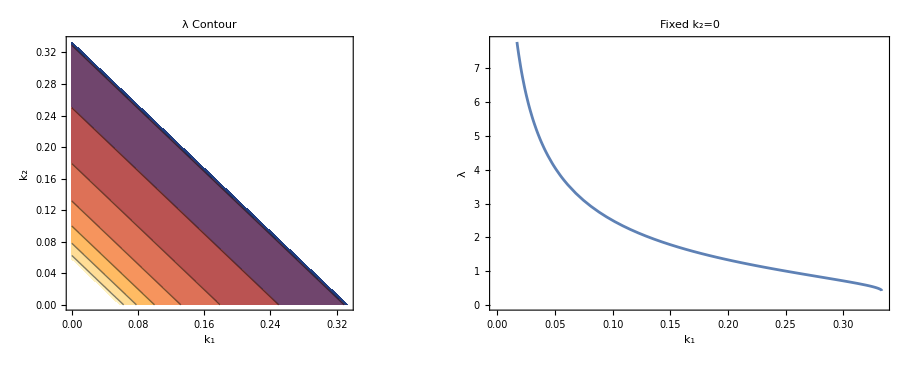

```mathematica
GraphicsRow[{ContourPlot[λ,{k1,0,1/3},{k2,0,1/3},FrameLabel->{Style["k_1",15],Style["k_2",15]}, PlotLabel->Style["λ Contour",15]],Plot[λ/.{k2->0},{k1,0,1/3},Frame->True,FrameLabel->{Style["k_1",15],Style["λ",15]},PlotLabel->Style["Fixed k_2=0",15]]}]
```

#### Key observations: k1 and k2 have the same contributions despite introducing different couplings

Hypothesis: cross terms do not contribute to alignment

### Building the θ_3 potential (the complete case)

The renormalizable terms stay the same, the dim 6 term should include every possible contractions that produces a trivial singlet

Recall that 1_(r,s) transforms as 1_(r,s)->ω^(r-s)1_(r,s), so for three singlets to be invariant we require 1_(r,s)1_(r',s')1_(r'',s'')->ω^((r+r'+r'')-(s+s'+s''))1_(r,s)1_(r',s')1_(r'',s'')

#### Find the combination of (r,s)^3 that satisfies (r+r'+r'')-(s+s'+s'')=0 mod 3

```mathematica
r=Table[{q,0,2},{q,{r1,r2,r3,s1,s2,s3}}];
Flatten[Table[{r1,r2,r3,s1,s2,s3},{r1,0,2},{r2,0,2},{r3,0,2},{s1,0,2},{s2,0,2},{s3,0,2}],5];
combo=Select[%,Mod[Total[#[[1;;3]]]-Total[#[[4;;6]]],3]==0&];
comboMap=Table[Thread[{r1,r2,r3,s1,s2,s3}->value],{value,combo}];
Print["There are ",Length[%]," terms"]
```

There are 243 terms

```mathematica
V2p2p2ALL=Sum[k singletProduct27[r1,s1,θ3,θ3]singletProduct27[r2,s2,θ3,θ3]singletProduct27[r3,s3,θ3,θ3]/.map,{map,comboMap}]/.sub27;
```

Let’s see if (0,0,v3) still minimises the potential

```mathematica
eqn=Table[D[VdimUpTo4+V2p2p2ALL,v]==0,{v,{t30,t31,t32}}]/.{t30->0,t31->0}
(*Solve[eqn,{t30,t31,t32},Assumptions->{m3>0,h3<0,k>0}]*)
```

```mathematica
Reduce[eqn,t32];
FullSimplify[%,Assumptions->{ω==E^(2 Pi I/3),t32!=0,h3<0}]
```

(t32==-(ⅈ m3)/(√2 √h3)||t32==(ⅈ m3)/(√2 √h3))&&k==0

The case of equal contribution from all dim 6 terms has no trivial solutions
Having all possible dim 6 terms break the (0,0,1) alignment
There are 243 terms, how do we classify them? What is the minimum amount of parameter we need to retain (0,0,1)